## Scattering calculations using numerical integration

### example: Yukawa potential V=g ⅇ^-m_0r/r

ⅆ_r^2 P+k^2 P=(2μ)/ℏ^2 V P
pick scaling length r=s Λ
ⅆ_s^2 P+(k Λ)^2 P=(2μ Λ^2)/ℏ^2 g ⅇ^(-m_0Λ s)/(s Λ) P
pick Λ=1/m_0, k_s=k Λ, g_s=(μ Λ g)/ℏ^2=(μ g)/(m_0 ℏ^2)
ⅆ_s^2 P+k_s^2 P=2 g_s ⅇ^(- s)/s P
Note that since there are 2 energy scales in this problem, a numerical value for g_s must be given.  We pick g_s=-17.

```mathematica
SE[k_]=With[{g=-17},p''[s]+k^2 p[s]==2 g ⅇ^-s p[s]]
```

k^2 p[s]+p''[s]==-34 ⅇ^-s p[s]

First, calculate the scattering length: at large 	r P=A(s-a_s), P'=A→ a_s=s-P/P'

```mathematica
sm=40;p0[s_]=NDSolve[{SE[0],p[0]==0,p'[0]==1},p[s],{s,0,sm}]⟦1,1,2⟧
```

InterpolatingFunction[{{0., 40.}}, <>][s]

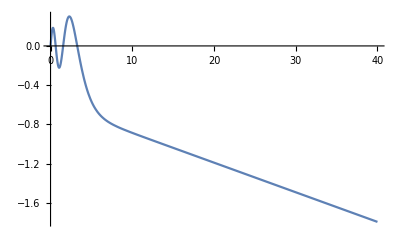

```mathematica
Plot[p0[s],{s,0,sm}]
```

```mathematica
sm-p0[sm]/p0'[sm]
```

-19.3963

```mathematica
σ0=4π %^2
```

4727.7

so the scattering length is a=-19.3 Λ and the cross section is σ=4727 Λ^2.  From the zero energy wavefunction, we deduce that there are 3 bound states in this potential

next, we calculate the phase shift for various k_s

```mathematica
δ[k_]:=Module[{},pk[s_]=NDSolve[{k^2 p[s]+p''[s]==-34 ⅇ^-s p[s],p[0]==0,p'[0]==1},p[s],{s,0,sm}]⟦1,1,2⟧;
Mod[ArcCot[pk'[sm]/(k pk[sm])]-k sm,π]]
```

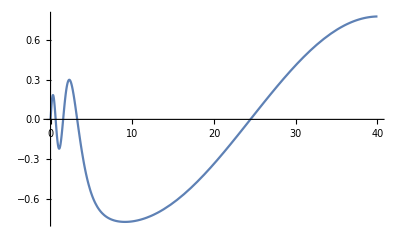

```mathematica
δ[.1];Plot[pk[s],{s,0,sm}]
```

```mathematica
ks=10^Range[-3,2,.03];
```

```mathematica
σs=Table[{k^2,Sin[δ[k]]^2(4π)/k^2},{k,ks}];
```

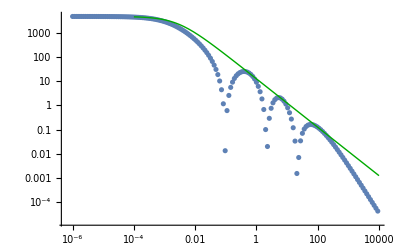

```mathematica
Show[ListLogLogPlot[σs],LogLogPlot[σ0/(1+σ0 ksq/(4π)),{ksq,.0001,10^4},PlotStyle->{Thick,Darker[Green]}]]
```